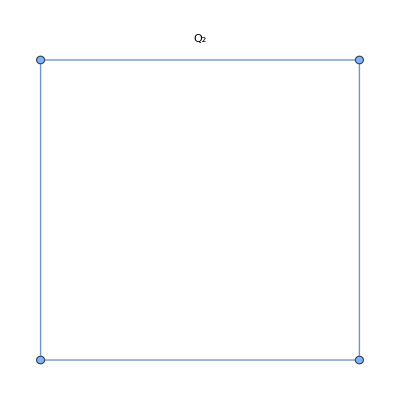
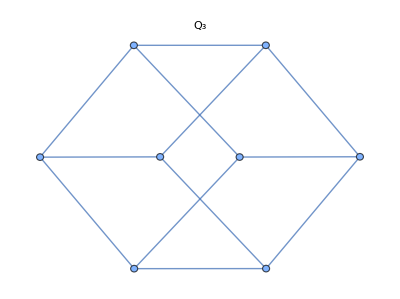
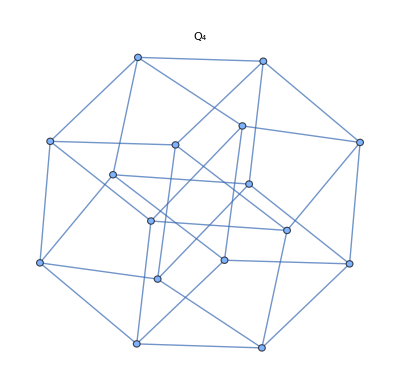
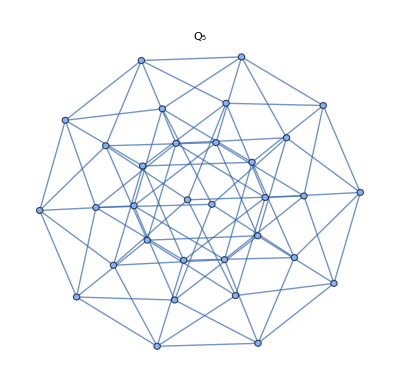

```mathematica
Table[HypercubeGraph[i,PlotLabel->Subscript[Q, i]],{i,2,5}]
```

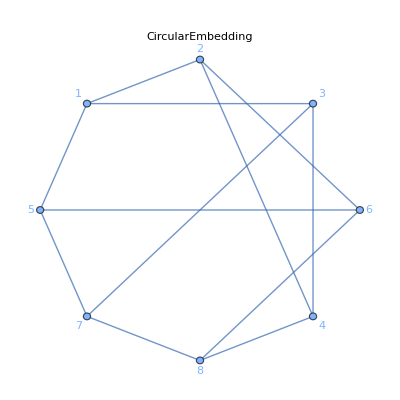
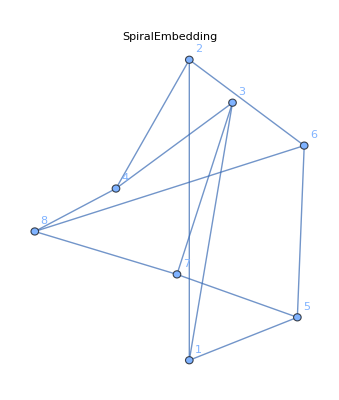
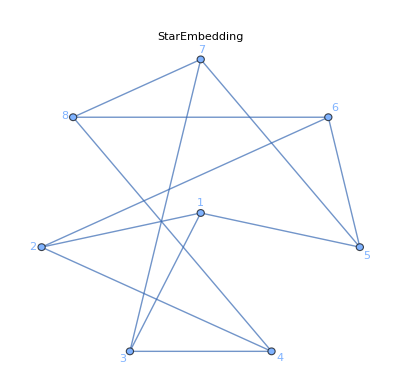
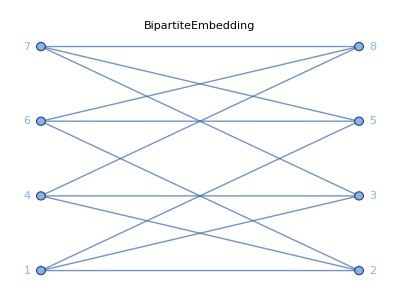
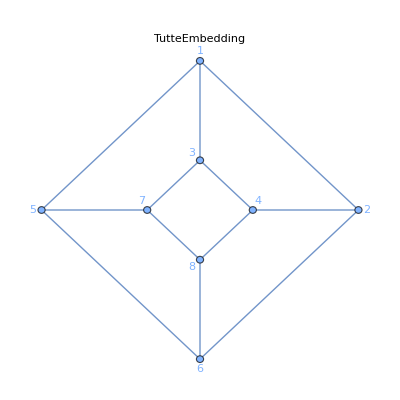

```mathematica
Table[HypercubeGraph[3,VertexLabels->"Name",GraphLayout->l,PlotLabel->l],{l,{"CircularEmbedding","SpiralEmbedding","StarEmbedding","BipartiteEmbedding","TutteEmbedding"}}]
```

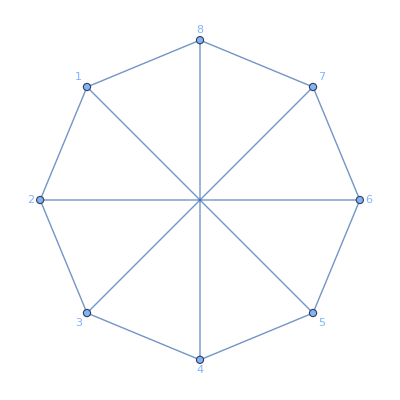

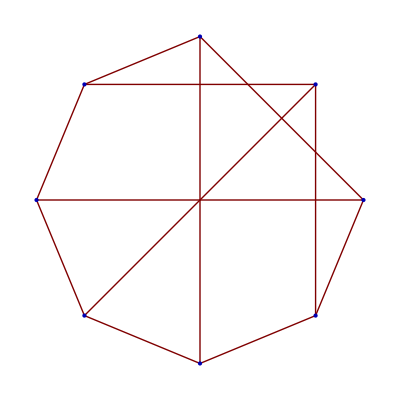

{{{1,2}},{{1,3,5}}}

True

{<|1→1,2→2,3→6,4→5,5→4,6→3,7→7,8→8|>}

```mathematica
ci8=CirculantGraph[8,{1,4},VertexLabels->"Name"]
g=EdgeAdd[CycleGraph[8],{1->4,2->6,3->7,5->8}];
GraphPlot[g,VertexLabels->"Name",VertexCoordinates->CircleLayout[8]]
{FindClique[g],FindIndependentVertexSet[g]}
IsomorphicGraphQ[ci8,g]
FindGraphIsomorphism[ci8,g]
```

```mathematica
Image3D[Rescale[ResourceFunction["MagicCube"][3]]]
```

-Graphics3D-

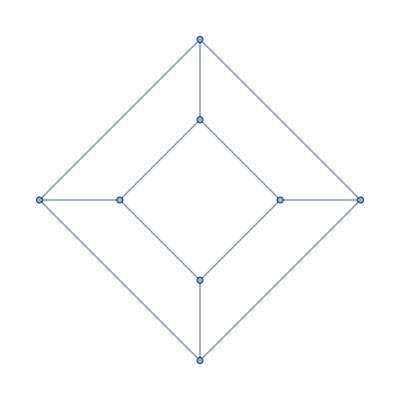

```mathematica
g=PetersenGraph[4,1]
```